# Pyramidal Stereo

Needs to import everything from folder “Methods” and “Tools”

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
SetDirectory[NotebookDirectory[]];
$Path=Append[$Path,FileNames["*",{ParentDirectory[]}]];
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\OpticalFlow - Copy\1DPackage\PyramidalStereo

```mathematica
<<"pyramid1d`"
```

## Images Analysis

```mathematica
move[im_,dx_]:=ImagePerspectiveTransformation[im,TranslationTransform[{dx,0}],DataRange->Full,Padding->"Reflected"]
showMove[ia_,ib_,{lowdx_,highdx_}]:=Manipulate[Show[Abs[ia-move[ib,dx]], ImageSize->Medium],{dx,lowdx,highdx}];

move::usage="
Input-> [im, dx]
Output -> image deplaced by dx
";

showMove::usage="
Input->[ia, ib, {lowdx, highdx}]
Output-> Manipulate object deplacing ia in range of lowdx and highdx with static ib
";
```

### Test

```mathematica
i=-Graphics-;
id=ImageDimensions[i]

iaa=ImageTake[i, {1,id[[2]]},{1,id[[1]]/2-15}];
ibb=ImageTake[i, {1,id[[2]]},{id[[1]]/2+16,id[[1]]}];
ia=ImageResize[iaa,ImageDimensions[iaa]/3];
ib=ImageResize[ibb,ImageDimensions[ibb]/3];

ic=move[ia,-0.4];

{ia,ib,ic}=ColorConvert[#,"Grayscale"]&/@{ia,ib,ic};
ImageDimensions[#]&/@{ia,ib,ic}

Show[GraphicsRow[{ia,ib}]]
```

{1200,730}

{{195,243},{195,243},{195,243}}

-Graphics-

```mathematica
showMove[ia,ib,{-1,40}]
```

### Test 2

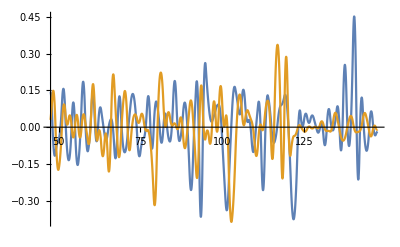
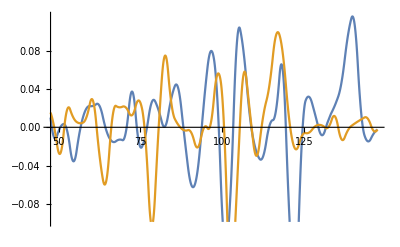
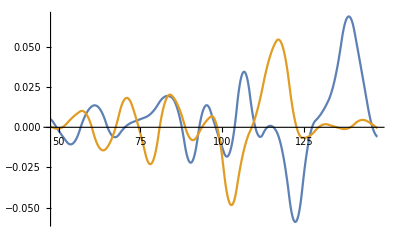
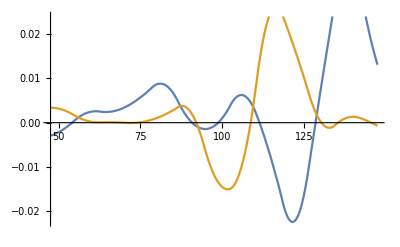
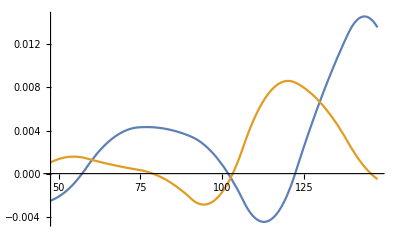
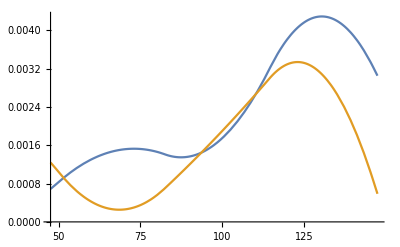

```mathematica
lvl=5;

{ka,kb}=ImageData[#][[100]]&/@{ia,ib};
pyra=pyrFuncGen[ka,lvl];
pyrb=pyrFuncGen[kb,lvl];
pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];

imd=Length[ka];

Table[Plot[{pyra[[n,2]][x],pyrb[[n,2]][x]},{x,imd/2 -50,imd/2 +50}],{n,1,lvl+1}]
```

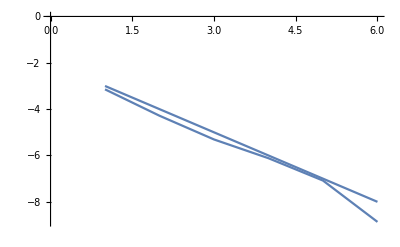

```mathematica
(* Log error *)
Show[
ListPlot[Log[2,StandardDeviation/@Table[pyra[[n,2]][x],{n,1,6},{x,100,imd}]],Joined->True],
Plot[-x-2,{x,1,6}]
]
```

## Solving for all y’s

```mathematica
stereoDepth[ia_,ib_,lvl_,{lvlmin_,lvlmax_},rangex_,rangey_,threshold_, mode_]:=Block[{ka,kb,pyra,pyrb,pyrab,thresholdAdj,dd,e,v1,v2},
thresholdAdj=threshold*2^(-lvlmin+1);

Get["pyramidalCyclope1DLK"<>mode<>"`"];

Table[

{ka,kb}=ImageData[#][[k]]&/@{ia,ib};
pyra=pyrFuncGen[ka,lvl];
pyrb=pyrFuncGen[kb,lvl];
pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];

Table[
If[mode=="OverConstrained",{v1,v2,dd}=PyrFlow1D[10,x,pyrab[[lvlmin;;lvlmax]],thresholdAdj],If[mode=="SemiConstrained",{v1,v2,dd}=PyrFlow1D[10,x,pyrab[[lvlmin;;lvlmax]],thresholdAdj],
If[mode=="SemiConstrainedErrorZero",{v1,v2,dd}=PyrFlow1D[10,x,pyrab[[lvlmin;;lvlmax]],thresholdAdj],{v1,v2,dd,e}=PyrFlow1D[10,x,pyrab[[lvlmin;;lvlmax]],thresholdAdj]]]];


{Total[{v1,v2}],dd,v1,v2}
,{x,rangex}]

,{k, rangey}]
]

stereoDepth[ia_,ib_,lvl_,mode_]:=stereoDepth[ia,ib,lvl,{1,lvl},Range[1,ImageDimensions[ia][[1]],1],Range[1,ImageDimensions[ia][[2]],1],0.0001,mode]
stereoDepth[ia_,ib_,lvl_,{lvlmin_,lvlmax_},threshold_,mode_]:=stereoDepth[ia,ib,lvl,{lvlmin,lvlmax},Range[1,ImageDimensions[ia][[1]],1],Range[1,ImageDimensions[ia][[2]],1],threshold,mode]

stereoDepth::usage="
Input=[ia, ib, lvl,{lvlmin,lvlmax},threshold, mode]
Output= {v, status, v1, v2}
ia= image a
ib= image b
lvl= max lvls to compute 
threshold= threshold for magnitude constraint
mode= method to calculate optical flow
";
```

### Test Graphs

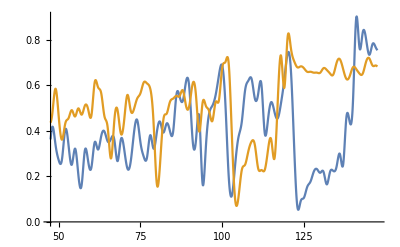
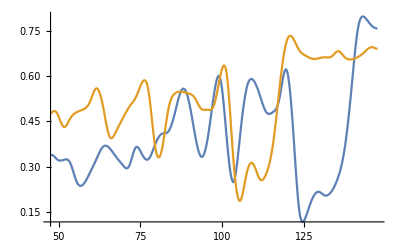
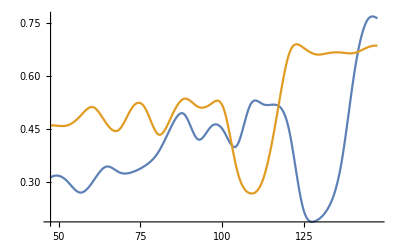
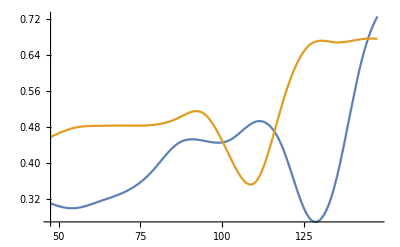
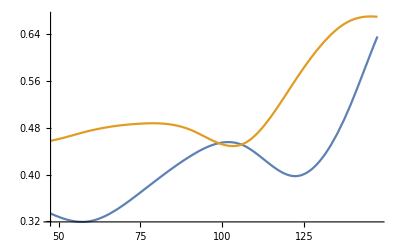
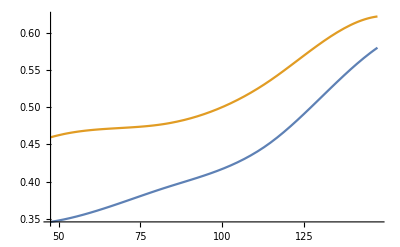

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[{pyra[[n,1]][x],pyrb[[n,1]][x]},{x,imd/2 -50,imd/2 +50}],{n,1,lvl+1}]
Table[Plot[{pyra[[n,2]][x],pyrb[[n,2]][x]},{x,imd/2 -50,imd/2 +50}],{n,1,lvl+1}]
```

### Tests OverConstrained

```mathematica
(*
"Constrained"
"SemiConstrained"
"OverConstrained"
*)
```

```mathematica
solution1=stereoDepth[ia,ib,5,{1,5},0.01,"OverConstrained"];
Dimensions[solution1]
```

{243,195,4}

```mathematica
disparitymap=Image[Rescale[solution1[[All,All,1]],{-50,0},{0,1}]];
Show[GraphicsRow[{disparitymap,ia,ib}],ImageSize->Large]
```

-Graphics-

### Tests SemiConstrained

```mathematica
solution2=stereoDepth[ia,ib,5,{1,5},0.01,"SemiConstrained"];
Dimensions[solution2]
```

$Aborted

{243,195,4}

```mathematica
disparitymap=Image[Rescale[solution2[[All,All,1]],{-50,0},{0,1}]];
Show[GraphicsRow[{disparitymap,ia,ib}],ImageSize->Large]
```

-Graphics-

### Tests Constrained

```mathematica
solution3=stereoDepth[ia,ib,5,{1,5},0.01,"Constrained"];
Dimensions[solution3]
```

$Aborted

{}

```mathematica
disparitymap=Image[Rescale[solution3[[All,All,1]],{-50,0},{0,1}]];
Show[GraphicsRow[{disparitymap,ia,ib}],ImageSize->Large]
```

-Graphics-